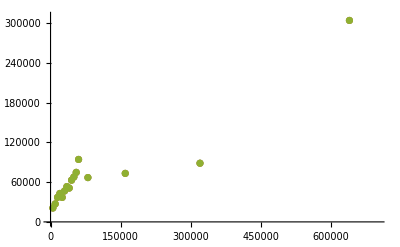

```mathematica
x = {5000, 10000,15000, 20000, 25000, 30000, 35000, 40000,45000, 50000, 55000,60000, 80000, 160000, 320000, 640000};
y = {20950, 27130, 37030, 42910, 36960, 46650, 53280, 51060, 62960, 67790, 74720, 94240, 66880, 73190, 88540, 303980};
std = {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}/Sqrt[10];
ListPlot[  {Transpose[{x,y}], Transpose[{x, y+0}],Transpose[{x, y-0}]  }, PlotRange-> {{0, 700000},{0, 310000}}]
```

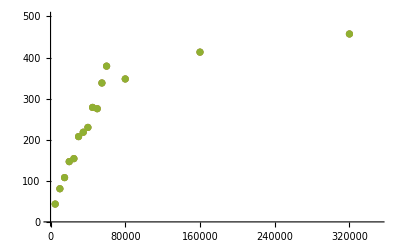

```mathematica
x  ={5000, 10000,15000, 20000, 25000, 30000, 35000, 40000,45000, 50000, 55000,60000, 80000, 160000, 320000};
roundcounts={43.4, 80.7, 107.8, 146.7, 154, 207.6, 218.2, 229.9, 278.6, 275.5,338.1, 379.1, 347.9, 413.2, 457.4};
ListPlot[{Transpose[{x,roundcounts}], Transpose[{x,roundcounts+0}],Transpose[{x, roundcounts-0}]  }, PlotRange-> {{0, 350000},{0, 500}}]
```

```mathematica
Length[x]
```

23

```mathematica
Length[roundcounts]
```

24

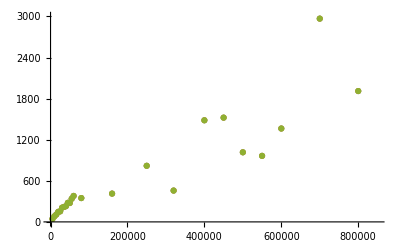

```mathematica
x  ={5000, 10000,15000, 20000, 25000, 30000, 35000, 40000,45000, 50000, 55000,60000, 80000, 160000, 250000, 320000, 400000, 450000, 500000, 550000, 600000, 700000, 800000};
roundcounts={43.4, 80.7, 107.8, 146.7, 154, 207.6, 218.2, 229.9, 278.6, 275.5,338.1, 379.1, 347.9, 413.2, 819.2, 457.4, 1483.9, 1522.5, 1016.4, 964.3, 1363.6, 2968.3, 1910.7};
ListPlot[{Transpose[{x,roundcounts}], Transpose[{x,roundcounts+0}],Transpose[{x, roundcounts-0}]  }, PlotRange-> {{0, 850000},{0, 3000}}]
```

{16.3416,38.4217,82.0386,98.3217,159.656,192.709,236.418,293.465,419.793,360.884,272.863,592.341,859.935,1078.53,563.997,729.913,621.808,997.814}

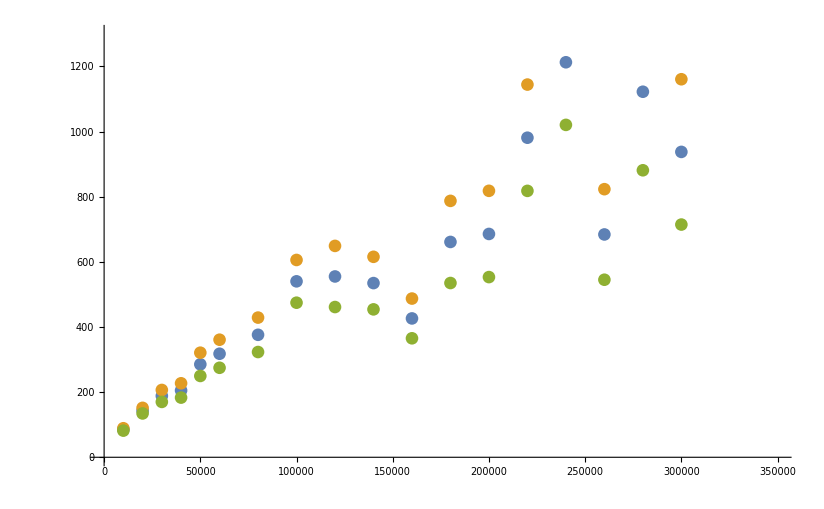

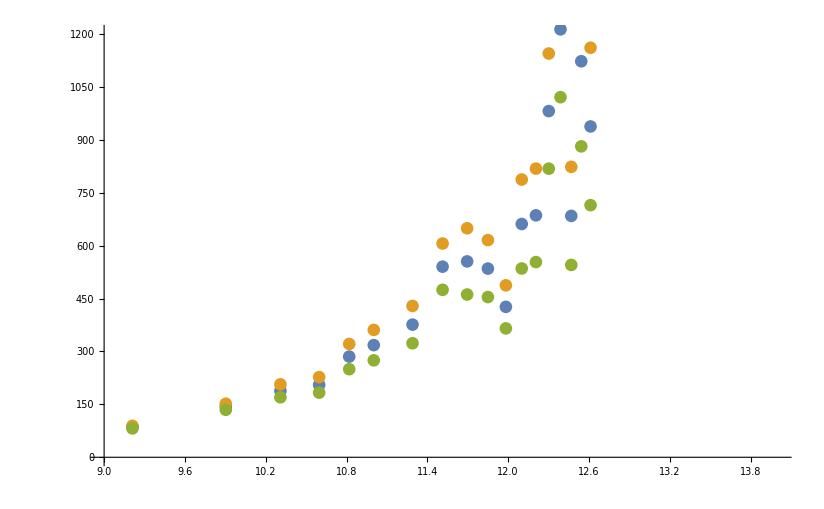

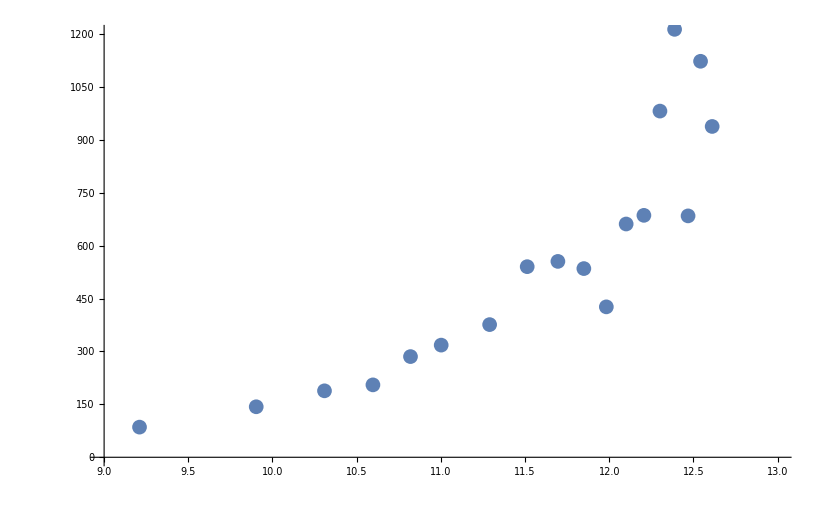

```mathematica
Ns = {10000,20000,30000,40000,50000,60000,80000,100000,120000,140000,160000,200000,240000,280000,180000,220000,260000,300000,320000};
roundcounts = {85.45,143.15,188.35,205.2,285.4,317.9,376.05,540.25,555.2,534.85,426.35,685.75,1212.95,1122.45,661.2,981.25,684.2,937.7};
std = {16.341588050125363,38.421706104752815,82.03857324454151,98.32171682797245,159.65631838420927,192.70934071808767,236.41795088359933,293.4647977185679,419.7927583939485,360.8843686002485,272.8628364215251,592.3412762082345,859.9348507299841,1078.5322190365941,563.9965957344069,729.9133424592264,621.8081376115948,997.813765188675}
ListPlot[{Transpose[{Ns,roundcounts}] ,Transpose[{Ns,roundcounts+std/Sqrt[20]}], Transpose[{Ns,roundcounts-std/Sqrt[20]}]   }, PlotRange-> {{0, 350000},{0, 1300}}]
ListPlot[{Transpose[{Log[Ns],roundcounts}],Transpose[{Log[Ns],roundcounts+std/Sqrt[20]}],Transpose[{Log[Ns],roundcounts-std/Sqrt[20]}] }, PlotRange-> {{9, 14},{0, 1200}}]
ListPlot[{Transpose[{Log[Ns],roundcounts}]}, PlotRange-> {{9, 13},{0, 1200}}]
```